# Homework 11

## Exercise 1

The present value of the two period income is: 5000 + 5500/1.10

```mathematica
5000 + 5500/(1.1)
```

10000.

We choose the bundle (c_1, c_2) to maximize U such that c_1 + c_2 = 10000.

We set up the Lagrangian:

ℒ(c_1, c_2, λ) =ln(c_1) + ln(c_2) + λ c_1 + c_2 - 10000
ⅆℒ/ⅆλ = c_1 + c_2 - 10000 = 0
ⅆℒ/(ⅆ c_1) = 1/c_1 + λ c_1 = 0
ⅆℒ/(ⅆ c_2) = 1/c_2 + λ c_2 = 0

```mathematica
Solve[c1 + c2 - 10000 == 0 && 1/c1 + λ*c1 == 0 && 1/c2 + λ c2 == 0,{c1, c2, λ}]
```

{{c1→5000,c2→5000,λ→-1/25000000}}

Or solving manually:
(first solve for λ)
1/c_1 + λ c_1 = 0
λ c_1 = -1/c_1
λ = -1/c_1^2
(Substitute into second expression)
1/c_2 + λ c_2 = 0
1/c_2 - c_2/c_1^2 = 0
1/c_2  = c_2/c_1^2
c_1^2 = c_2^2
±c_2 = ± c_1
(Substitute into constraint)
c_1 + c_2 = 10000
2 c_1 = 10000 or -2 c_1 = 10000
(c_1, c_2) = (5000, 5000)  or (c_1, c_2) = (-5000, -5000)
Second solution makes no economioc sense.
∴ (c_1, c_2) = (5000, 5000)

## Exercise 2

## Exercise 3

Prove λ(x + y) = λx + λy

Consider the vector (x + y).  The sum of the j^th element is (x_j + y_j).  Multiplying the vector (x + y) by λ, we obtain the vector λ(x + y), whose j^th element is λ(x_j + y_j) = λx_j + λy_j (by distributive property of multiplication over addition on the Reals).

Now consider the sum of the vector λx and λy: (λx + λy).  The j^th element of λx is λx_j and of λy is λy_j.  Therefore the sum of the j^th element is λx_j + λy_j.  Therefore the j^th row of λ(x + y) is the same as the j^th row of λx + λy.  Since j is an arbitrary row, this is true for the entire vector sum.

Prove (λ_1 + λ_2)x = λ_1x + λ_2x.

Consider the vector λ_1x. Its j^th element is given by λ_1 x_j.  Similarly for the vector λ_2x the j^th element is given by λ_1 x_j.  Thus the j^th row of the sum of the vectors λ_1x + λ_2x is given by: λ_1 x_j + λ_2 x_j = λ_1 + λ_2 x_j = (λ_1 + λ_2) x_j (by the distributive property of multiplication over addition on reals).  Since x_j is arbitrary, this holds for the entire vector, that is λ_1x + λ_2x = (λ_1 + λ_2) x.

## Exercise 4

Base case
Let n = 1.
S(1) = 1  = 1^2.

Recursive case
If S(n-1) = (n-1)^2
Then S(n) = (n-1)^2 + (2n - 1)
(n-1) (n-1) + 2n + 1 = n^2 - 2n + 1 + 2n - 1 = n^2

## Computational Exercise 1

```mathematica
fact[0] := 1
fact[x_] := x*fact[x-1]
```

1

1

2

6

24

{{0,1},{1,1},{2,2},{3,6},{4,24},{5,120},{6,720}}

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36}}

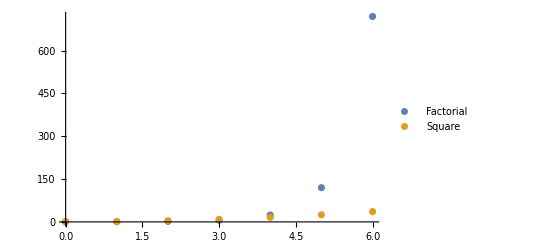

```mathematica
fact[0]
fact[1]
fact[2]
fact[3]
fact[4]
facts = {#, fact[#]}&/@Range[0, 6]
squares ={ #,#^2}&/@Range[0,6]
ListPlot[{facts,squares}, PlotRange->All, PlotLegends->{"Factorial", "Square"}]
```

The factorial function grows faster

## Computational Exercise 2

```mathematica
soln = Solve[1053.9*Exp[rIndia*10]==1224.6 &&  1269.1*Exp[rChina*10]==1341.3, {rIndia, rChina}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rIndia→0.0150117,rChina→0.00553313}}

```mathematica
Solve[(1053.9*Exp[rIndia*t] == 1269.1*Exp[rChina*t]/.soln), t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→19.6033}}

i.e. by 2020 India’s population will overtake China.

```mathematica
soln = Solve[2.53*^9 * Exp[r*(2015-1950)] == 7.3*^9, r]
proj = 2.53*^9 Exp[r*(2050-1950)]/.soln
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0.0163024}}

{1.29159×10^10}

i.e. 12.9 billion.

Carrying Capacity: the number of people, other living organisms, or crops that a region can support without environmental degradation. (source: dictionary.com)

Such a projection is not realistic. For example, while in the period before the 1980s the growth rate was higher than the average of 1.63%, growth rates have been steadily declining since then.  Thus, the average growth rate over the next 50 years are going to be much lower than the average growth rate over the last 50 years.  Here is the Census bureau’s projection on this:

-Graphics-

## Computational Exercise 4

Assume at t = 0 we start at q_0.
At t = 1, we are at:
q_1 = 0.86 q_0.
At t = 2, we are at:
q_2 = 0.86 q_1 = 0.86^2 q_0
and so on
therefore we have at t=n
q_n = 0.86^n q_0

```mathematica
Solve[q0*(0.86^n) == (1/2)q0, n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→4.59577}}

Therefore, after about 4.6, we will be at half the value from the deviation.

## Computational Exercise 5

the interest rate at which the net present value of all the cash flows from a project or investment equal zero.

```mathematica
project1 = Cashflow[{-100000.,60000,47000}]
project2 = Cashflow[{-100000.,50000,40000, 20000}]
irr1 = Solve[{TimeValue[project1, i1, 0]==0, i1 ≥0}, {i1}]
irr2 = Solve[{TimeValue[project2, i2, 0]==0, i2≥0}, {i2}]
```

Cashflow[{-100000.,60000,47000}]

Cashflow[{-100000.,50000,40000,20000}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i1→0.0483315}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i2→0.0572597}}

Pick project that pays the stream {50000,40000, 20000} since this has a higher IRR (5.7% vs. for other project 4.8%).

```mathematica
project1a = Cashflow[{-90000.,60000,47000}]
project2a = Cashflow[{-90000.,50000,40000, 20000}]
irr1 = Solve[{TimeValue[project1a, i1, 0]==0, i1 ≥0}, {i1}]
irr2 = Solve[{TimeValue[project2a, i2, 0]==0, i2≥0}, {i2}]
```

Cashflow[{-90000.,60000,47000}]

Cashflow[{-90000.,50000,40000,20000}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i1→0.129156}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i2→0.125722}}

With a fall in the inital investment to 90000, the project paying {60000, 47000} now has a higher IRR (12.9% vs. other project which makes 12.6%).

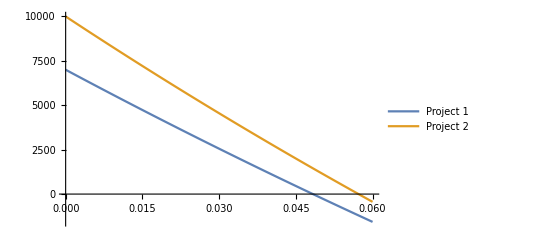

```mathematica
Plot[{TimeValue[project1, r, 0], TimeValue[project2, r, 0]}, {r, 0, 0.06}, PlotLegends->{"Project 1", "Project 2"}]
```

## Computational Exercise 6

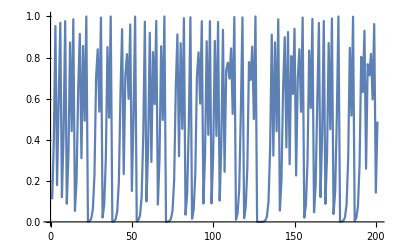

```mathematica
ListLinePlot[NestList[4#(1-#)&, 0.11, 200]]
```

## Computational Exercise 7

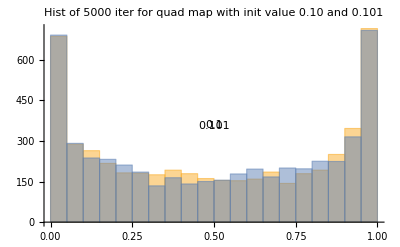

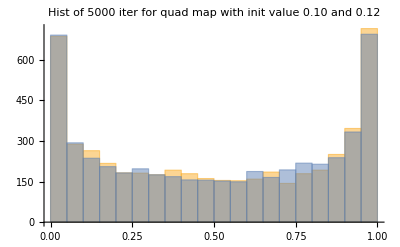

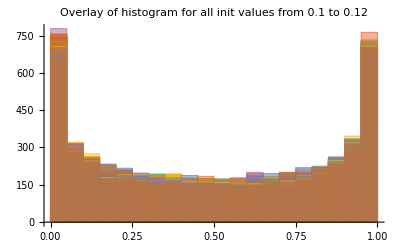

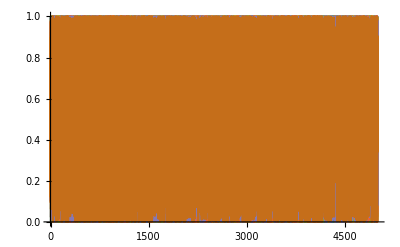

```mathematica
res = NestList[4#(1-#)&, #, 5000]& /@ Range[0.10, 0.12, .001];
Histogram[{res[[1]], res[[2]]}, ChartLabels->Placed[Range[0.1, 0.12,0.001],Center],PlotRange->All,PlotLabel->"Hist of 5000 iter for quad map with init value 0.10 and 0.101" ]
Histogram[{res[[1]], res[[20]]}, PlotLabel->"Hist of 5000 iter for quad map with init value 0.10 and 0.12"]
Histogram[res, PlotLabel->"Overlay of histogram for all init values from 0.1 to 0.12"]
ListLinePlot[res]
```

Comments:  We get every number between 0 and 1 but a bunching up near 0 and 1.

```mathematica
myEuclideanDistance[x_, y_] := Sqrt[Total[MapThread[(#2-#1)^2&, {y, x}]]]

myEuclideanDistance[{1}, {5}] (* test my function *)
EuclideanDistance[{1}, {5}] (* test built in function *)

myEuclideanDistance[{1, 2}, {5, 6}] (* test my function *)
EuclideanDistance[{1, 2}, {5, 6}]

myEuclideanDistance[{1, 2, 3}, {5, 6, 7}] (* test my function *)
EuclideanDistance[{1, 2, 3}, {5, 6, 7}] (* test built in function *)

myEuclideanDistance[{1, 2, 3, 4}, {5, 6, 7, 8}] (* test my function *)
EuclideanDistance[{1, 2, 3, 4}, {5, 6, 7, 8}] (* test built in function *)

myEuclideanDistance[{1, 2}, {5, 6, 7}] (* test my function *)
EuclideanDistance[{1, 2}, {5, 6, 7}] (* test built in function *)
```

4

4

4 √2

4 √2

4 √3

4 √3

8

8

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[(#2-#1)^2&,{{5,6,7},{1,2}}]; dimensions are 3 and 2.

{{√(5+((#2-#1)^2&)),√(6+((#2-#1)^2&)),√(7+((#2-#1)^2&))},{√(1+((#2-#1)^2&)),√(2+((#2-#1)^2&))}}

EuclideanDistance[{1,2},{5,6,7}]

## Computational Exercise 9

```mathematica
seq = Array[0.8^#&, 21, 0]
```

{1.,0.8,0.64,0.512,0.4096,0.32768,0.262144,0.209715,0.167772,0.134218,0.107374,0.0858993,0.0687195,0.0549756,0.0439805,0.0351844,0.0281475,0.022518,0.0180144,0.0144115,0.0115292}

```mathematica
ser = FoldList[Plus, seq]
```

{1.,1.8,2.44,2.952,3.3616,3.68928,3.95142,4.16114,4.32891,4.46313,4.5705,4.6564,4.72512,4.7801,4.82408,4.85926,4.88741,4.90993,4.92794,4.94235,4.95388}

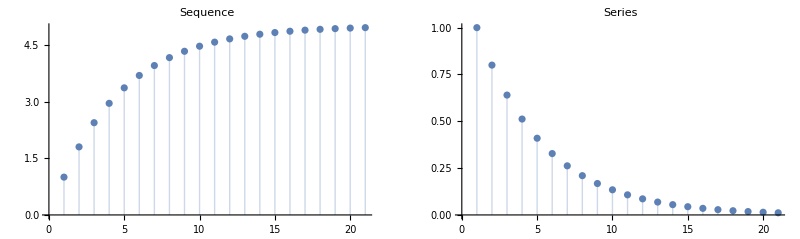

```mathematica
GraphicsRow[{ListPlot[ser, PlotLabel->"Sequence", Filling->Axis], ListPlot[seq, PlotLabel->"Series", Filling->Axis]}]
```